```mathematica
Needs["JLink`"]
InstallJava[]
AddToClassPath[NotebookDirectory[]]
```

LinkObject[…]

{C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload\PacletManager\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload\PacletManager\Java\antlr.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload\PacletManager\Java\mexpr.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload\PacletManager\Java\mexprparser.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Autoload\PacletManager\Java\PacletManager.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\activation.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\bzip2.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\commons-codec-1.15.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\commons-collections4-4.4.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\commons-compress-1.21.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\commons-io-2.11.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\commons-lang-2.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\commons-logging-1.2.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\commons-math3-3.6.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\Convert.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\customizer.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\dom4j-2.1.4.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\Exif.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\externalservice.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\gnu-regexp-1.1.4.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\grib-8.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\jackcess-2.1.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\jdbf.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\jdom.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\jmf.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\JPEG2000b.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\JSON.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\jxl.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\ldap.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\mail.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\mediaplayer.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\multiplayer.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\netcdf-4.2.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\poi-5.2.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\poi-ooxml-5.2.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\poi-ooxml-lite-5.2.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\prefsAll.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\resourcesOptional.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\SparseBitSet-1.2.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\tagsoup-1.2.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\tar.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\xercesImpl.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\xml-apis.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Converters\Java\xmlbeans-5.1.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\bsf-Wolfram.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\bsf.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\concurrent.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\diva-canvas-core.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\GUIKit.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\OculusLayout.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\xercesImpl.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Packages\GUIKit\Java\xmlParserAPIs.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\commons-collections4-4.4.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\commons-dbcp-1.4.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\commons-lang-2.6.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\commons-logging-1.1.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\commons-pool-1.6.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\derby.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\derbyclient.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\derbynet.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\derbyoptionaltools.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\derbyrun.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\derbyshared.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\derbytools.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\glazedlists.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\h2-2.1.214.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\hsqldb-2.7.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\jackcess-2.1.9.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\jaybird-full-3.0.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\jtds-1.3.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\log4j-api-2.20.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\log4j-core-2.20.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\logback-classic-1.4.7.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\logback-core-1.4.7.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\mariadb-java-client-3.1.2.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\mssql-jdbc-9.4.0.jre11.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\postgresql-42.6.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\sqlite-jdbc-3.36.0.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\DatabaseLink\Java\ucanaccess-4.0.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\RLink\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\RLink\Java\jna-5.8.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\RLink\Java\JRI.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\RLink\Java\JRIEngine.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\RLink\Java\REngine.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\RLink\Java\RLink.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\WebServices\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\WebServices\Java\commons-httpclient-3.0.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\WebServices\Java\commons-logging-1.0.4.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\WebServices\Java\junit-3.8.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\XMLSchema\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Links\XMLSchema\Java\commons-codec-1.3.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications\ClusterIntegration\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications\ClusterIntegration\Java\Wolfram_SGE.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications\DocumentationSearch\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications\LightweightGridClient\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\AddOns\Applications\LightweightGridClient\Java\wolfram-remote-services-client.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Chemistry\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Chemistry\Java\helm2-helmnotationparser-1.2.2.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Chemistry\Java\molvec-0.9.8-jar-with-dependencies.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Chemistry\Java\opsin-core-3.0-SNAPSHOT-jar-with-dependencies.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Chemistry\Java\opsin-document-extractor-1.1-SNAPSHOT.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Chemistry\Java\symmetrizer.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Chemistry\Java\WolframChemistryJava.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Interpreter\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Interpreter\Java\libphonenumber-8.12.14.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\Interpreter\Java\ParseTelephoneNumber.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Java\Windows-x86-64\lib\tools.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\javaBuild,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\antlr.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\antlr4-runtime-4.5.1-1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\asm-8.0.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\asm-commons-8.0.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\hppc-0.8.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-analyzers-common-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-analyzers-kuromoji-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-analyzers-smartcn-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-backward-codecs-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-core-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-expressions-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-facet-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-highlighter-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-memory-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-queries-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-queryparser-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-spatial3d-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\lucene-suggest-8.10.1.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\mexpr.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\mexprparser.jar,C:\Program Files\Wolfram Research\Mathematica\14.0\SystemFiles\Components\TextSearch\Java\TextSearch.jar,C:\Users\danmc\IdeaProjects\MultiplicativeECA\out\production\MultiplicativeECA\}

```mathematica
ecam = JavaNew["ECAasMultiplication"]
```

«JavaObject[ECAasMultiplication]»

```mathematica
tables = ecam@generateMultTable[0,2,3]
```

{{{0,1,2,3,4,5,6,7},{1,4,7,2,5,0,3,6},{2,3,4,5,6,7,0,1},{3,6,1,4,7,2,5,0},{4,5,6,7,0,1,2,3},{5,0,3,6,1,4,7,2},{6,7,0,1,2,3,4,5},{7,2,5,0,3,6,1,4}},{{0,2,1,3,4,6,5,7},{2,4,7,1,6,0,3,5},{1,3,4,6,5,7,0,2},{3,5,2,4,7,1,6,0},{4,6,5,7,0,2,1,3},{6,0,3,5,2,4,7,1},{5,7,0,2,1,3,4,6},{7,1,6,0,3,5,2,4}},{{0,2,1,3,4,6,5,7},{2,4,3,5,6,0,7,1},{1,7,4,2,5,3,0,6},{3,1,6,4,7,5,2,0},{4,6,5,7,0,2,1,3},{6,0,7,1,2,4,3,5},{5,3,0,6,1,7,4,2},{7,5,2,0,3,1,6,4}},{{0,1,2,3,4,5,6,7},{1,4,3,6,5,0,7,2},{2,7,4,1,6,3,0,5},{3,2,5,4,7,6,1,0},{4,5,6,7,0,1,2,3},{5,0,7,2,1,4,3,6},{6,3,0,5,2,7,4,1},{7,6,1,0,3,2,5,4}}}

```mathematica
specific = ecam@specific
```

«JavaObject[ECAMspecific]»

```mathematica
wCode = {0,1,1,1,1,0,0,0}
```

{0,1,1,1,1,0,0,0}

```mathematica
specific@generalWolframCode[wCode,5,tables,0]
```

```mathematica
solutions = specific@validSolutions
```

{«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»,«JavaObject[ValidSolution]»}

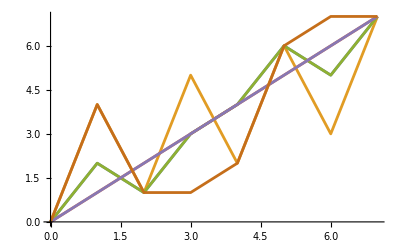

```mathematica
ListPlot[solutions[[50]]@factors, Joined ->True, DataRange->{0,7}]
```